# Updated Supervised Machine Learning

ResNet-50 trained on image classification was used for the supervised learning of the weeds Annual Sowthistle and Little Mallow consisting of a training data set of 429 and testing set of 106. We received an accuracy of 84% accuracy with a 17% baseline. The accuracy acquired from this model depends on the quality of the training set from where the neural network learns the parameters to apply to the testing set.

## Imported Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/Desktop/Weeds_Project

```mathematica
"/home/student/Weeds_Project"
```

/home/student/Weeds_Project

```mathematica
droughtAS=Import["./Weed_Images/Digital_Camera/Annual_Sowthistle/Drought_Images/*.JPG"];
```

```mathematica
highFertilityAS=
Import["./Weed_Images/Digital_Camera/Annual_Sowthistle/High_Fertility_Images/*.JPG"];
```

```mathematica
injuredAS=Import["./Weed_Images/Digital_Camera/Annual_Sowthistle/Injury_Images/*.JPG"];
```

```mathematica
standardAS=Import["./Weed_Images/Digital_Camera/Annual_Sowthistle/Standard_Images/*.JPG"];
```

```mathematica
droughtLM=Import["./Weed_Images/Digital_Camera/Little_Mallow/Drought_Images/*.JPG"];
```

```mathematica
highFertilityLM=Import["./Weed_Images/Digital_Camera/Little_Mallow/High_Fertility_Images/*.JPG"];
```

```mathematica
injuredLM=Import["./Weed_Images/Digital_Camera/Little_Mallow/Injury_Images/*.JPG"];
```

```mathematica
standardLM=Import["./Weed_Images/Digital_Camera/Little_Mallow/Standard_Images/*.JPG"];
```

## Labeled Data

```mathematica
droughtLAS=Thread[droughtAS->"DAS"];
```

```mathematica
droughtLLM=Thread[droughtLM->"DLM"];
```

```mathematica
highFertilityLAS=Thread[highFertilityAS->"HFAS"];
```

```mathematica
highFertilityLLM=Thread[highFertilityLM->"HFLM"];
```

```mathematica
injuredLAS=
Thread[injuredAS->"IAS"];
```

```mathematica
injuredLLM=Thread[injuredLM->"ILM"];
```

```mathematica
standardLAS=Thread[standardAS->"SAS"];
```

```mathematica
standardLLM=Thread[standardLM->"SLM"];
```

## Training Testing Data Split (80 tr/20 te)

```mathematica
ResourceFunction["TrainTestSplit"]
```

```mathematica
{trainDAS,testDAS}=[droughtLAS];
```

```mathematica
{trainDLM,testDLM}=[droughtLLM];
```

```mathematica
{trainHFAS,testHFAS}=[highFertilityLAS];
```

```mathematica
{trainHFLM,testHFLM}=[highFertilityLLM];
```

```mathematica
{trainIAS,testIAS}=[injuredLAS];
```

```mathematica
{trainILM,testILM}=[injuredLLM];
```

```mathematica
{trainSAS,testSAS}=[standardLAS];
```

```mathematica
{trainSLM,testSLM}=[standardLLM];
```

## Combined Trained and Test data

```mathematica
totalTrainData=Join[trainDAS,trainDLM,trainHFAS,trainHFLM,trainILM,trainIAS,trainSAS,trainSLM];
```

```mathematica
totalTestData=Join[testDAS,testDLM,testHFAS,testHFLM,testILM,testIAS,testSAS,testSLM];
```

## Imported Neural Network and Removed Layers for learning

```mathematica
tempNet=Take[NetModel["ResNet-50 Trained on ImageNet Competition Data"],{1,-4}]
```

NetChain[<22>]

## Supervised Classes

```mathematica
newNet=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[8],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"SAS","SLM","DAS","DLM","IAS","ILM","HFAS","HFLM"}}]]
```

NetChain[<3>]

## Training Neural Network

```mathematica
trainedNet=NetTrain[newNet,totalTrainData,LearningRateMultipliers->{"linearNew"->1,_->0},TargetDevice->"GPU",BatchSize->2]
```

NetChain[<3>]

## Data Analysis

```mathematica
ClassifierMeasurements[trainedNet,totalTestData,"Accuracy"]
```

0.811321

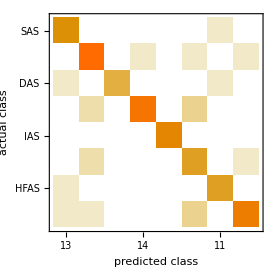
Classifier Measurements
Classifier method | Net
Number of test examples | 106
Accuracy | (81.4.) %
Accuracy baseline | (17.4.) %
Geometric mean of probabilities | 0.612 ± 0.047
Mean cross entropy | 0.492 ± 0.076
Single evaluation time | 278. ms/example
Batch evaluation speed | 8.77 examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[trainedNet,totalTestData]
```

```mathematica
Length[totalTestData]
```

106

```mathematica
Length[totalTrainData]
```

429